# Algebraic Ground Truth Inference Penn ML Benchmarks demonstrations: twonorm

The Penn ML benchmark `twonorm` is a binary classification dataset. This is an artificial or synthetic dataset consisting of 7,400 20-dimensional vectors drawn from two Gaussian distributions. For this demonstration we took 1000 from each of the two labels as our training set and tested on the 5,400 remaining records (2,703 “0” + 2,697 “1”).

## Code

### Ingesting the data from Github and initializing the mushroom data table

```mathematica
datasetName="twonorm"
filename="https://github.com/EpistasisLab/penn-ml-benchmarks/blob/master/datasets/"<>datasetName<>"/"<>datasetName<>".tsv.gz?raw=true";
tsvHeader=Import[filename,"TSV"]//First;
benchmarkData=Import[filename,"TSV"]//Rest//GroupBy[#,Last]&//Map[Most,#,{2}]&;
```

twonorm

```mathematica
tsvHeader
numberOfFeatures=Length@tsvHeader-1
```

{A1,A2,A3,A4,A5,A6,A7,A8,A9,A10,A11,A12,A13,A14,A15,A16,A17,A18,A19,A20,target}

20

### Training/testing code

```mathematica
Clear[TrainClassifiers]
TrainClassifiers[classifiersData_,classifierTypes_List,nTrainTotal_Integer,nEachRandom_Integer]:=Module[
{ trainingSamples, classifiers},
(* All this code is standard Mathematica code.  The workhorse command is - Classify. We even just go with the default settings for
the algoritms Mathematica implements with it *)
(* Picking about 1/2 chance of overlap seems best with our current settings *)
trainingSamples=Table[RandomSample[Range@nTrainTotal,nEachRandom],{Length@classifiersData}];
classifiers=Transpose@{classifierTypes,Map[First,classifiersData,{2}]//MapIndexed[#1[[trainingSamples[[#2[[1]]]]]]&,#,{2}]&}//Map[Classify[#[[2]],Method->#[[1]],TrainingProgressReporting->None]&,#]&;
classifiers]
```

```mathematica
Clear[LabelRMSE]
LabelRMSE[gtDiff_,label_]:=KeySelect[gtDiff,(Length@#==3)&]//KeySelect[#,(Last@#==label)&]&//Values//Map[#^2&,#]&//Mean//Sqrt 
Clear[AlgebraicallyEvaluateClassifiers]
AlgebraicallyEvaluateClassifiers[classifiers_,classifiersData_]:=Module[
{nTestAlpha, nTestBeta, decisions, 
alphaSamples, betaSamples, 
byLabelDecisions, votingPatternCountsByLabel,
sols,equationsToSolve,vars,
gt,avgSol,gtDiff},
(* Calculate the size of the test sets *)
{nTestAlpha,nTestBeta}=classifiersData//First//Map[Length,#,{2}]&//{#[0],#[1]}&//Last/@#&;
(* We arbitrarily define "0" as the alpha label, and "1" as the beta label *)
decisions=Table[classifiers[[i]][classifiersData[[i]]//Map[Last,#]&//Join[#[0],#[1]]&],{i,Length@classifiers}];
alphaSamples=RandomSample[Range@nTestAlpha,nTestAlpha];
betaSamples=RandomSample[Range@nTestBeta,nTestBeta];
byLabelDecisions=decisions//Map[TakeDrop[#,2703]&,#]&//Map[Association[{0->#[[1]][[alphaSamples]],1->#[[2]][[betaSamples]]}]&,#]&;
votingPatternCountsByLabel=byLabelDecisions//Merge[#,Identity]&//Map[Transpose,#]&//Map[Counts,#]&;
Map[Length,votingPatternCountsByLabel];
 sols=Table[
equationsToSolve=MakeIndependentVotingIdeal[trio];
vars=Variables/@equationsToSolve//Flatten//DeleteDuplicates//Sort//Cases[#,Except[Subscript[f, __]]]&;
Solve[Map[(#==0)&,equationsToSolve]/.VotingFrequenciesData[votingPatternCountsByLabel,trio],vars]//N,
{trio,Subsets[Range@Length@classifiers,{3}]}];
gt=Join[{Subscript[P, α]->(votingPatternCountsByLabel//Map[Values,#]&//Map[Total,#]&//#[0]/Total@#&)},Table[Subscript[P,i,α]->DataGroundTruth[votingPatternCountsByLabel,0,i],{i,Length@classifiers}],Table[Subscript[P,i,β]->DataGroundTruth[votingPatternCountsByLabel,1,i],{i,Length@classifiers}]]//
Association;
avgSol=Select[sols,IsAPhysicalSolutionQ]//Map[PickHighestAverageAccuracy,#]&//Flatten//GroupBy[#,First]&//Map[Last,#,{2}]&//Map[Mean,#]&//KeySortBy[#,Last@#&]&;
gtDiff=Merge[{gt//N,-avgSol},Total];
{Subscript[P, α]/.gtDiff,LabelRMSE[gtDiff,α],LabelRMSE[gtDiff,β],gt,avgSol}
 ]
```

### Writing out the independent evaluation ideal generator set

```mathematica
Clear[MakeIndependentVotingIdeal]
MakeIndependentVotingIdeal[{i_,j_,k_}]:={Subscript[P, α] Subscript[P, i,α] Subscript[P, j,α] Subscript[P, k,α]+(1-Subscript[P, α]) (1-Subscript[P, i,β]) (1-Subscript[P, j,β]) (1-Subscript[P, k,β])-Subscript[f, α,α,α],Subscript[P, α] Subscript[P, i,α] Subscript[P, j,α] (1-Subscript[P, k,α])+(1-Subscript[P, α]) (1-Subscript[P, i,β]) (1-Subscript[P, j,β]) Subscript[P, k,β]-Subscript[f, α,α,β],Subscript[P, α] Subscript[P, i,α] (1-Subscript[P, j,α]) Subscript[P, k,α]+(1-Subscript[P, α]) (1-Subscript[P, i,β]) Subscript[P, j,β] (1-Subscript[P, k,β])-Subscript[f, α,β,α],Subscript[P, α] Subscript[P, i,α] (1-Subscript[P, j,α]) (1-Subscript[P, k,α])+(1-Subscript[P, α]) (1-Subscript[P, i,β]) Subscript[P, j,β] Subscript[P, k,β]-Subscript[f, α,β,β],Subscript[P, α] (1-Subscript[P, i,α]) Subscript[P, j,α] Subscript[P, k,α]+(1-Subscript[P, α]) Subscript[P, i,β] (1-Subscript[P, j,β]) (1-Subscript[P, k,β])-Subscript[f, β,α,α],Subscript[P, α] (1-Subscript[P, i,α]) Subscript[P, j,α] (1-Subscript[P, k,α])+(1-Subscript[P, α]) Subscript[P, i,β] (1-Subscript[P, j,β]) Subscript[P, k,β]-Subscript[f, β,α,β],Subscript[P, α] (1-Subscript[P, i,α]) (1-Subscript[P, j,α]) Subscript[P, k,α]+(1-Subscript[P, α]) Subscript[P, i,β] Subscript[P, j,β] (1-Subscript[P, k,β])-Subscript[f, β,β,α],Subscript[P, α] (1-Subscript[P, i,α]) (1-Subscript[P, j,α]) (1-Subscript[P, k,α])+(1-Subscript[P, α]) Subscript[P, i,β] Subscript[P, j,β] Subscript[P, k,β]-Subscript[f, β,β,β]}
```

```mathematica
Clear[DataGroundTruth]
DataGroundTruth[data_List,label_,classifier_Integer]:=Module[
{withoutHeaderData=Rest@data,byLabel},
byLabel=GroupBy[withoutHeaderData,#[[5]]&];
Map[#[[{1,2,3,4,7}]]&,byLabel,{2}]//
#[label]&//
Map[#[[{classifier,-1}]]&,#]&//
GroupBy[#,First]&//
Map[Last,#,{2}]&//
Total/@#&//
#[label]/Total@#&]
DataGroundTruth[data_Association,label_,classifier_Integer]:=Module[
{},
data[label]//Normal//Map[(#[[1]][[classifier]]->#[[2]])&,#]&//
Map[Association,#]&//Merge[#,Total]&//#[label]/Total@#&]
```

```mathematica
Clear[VotingFrequenciesData]
VotingFrequenciesData[data_List,classifiers:{_Integer,_Integer,_Integer}]:=Module[
{withoutHeaderData=Rest@data, eventCounts},
eventCounts=GroupBy[withoutHeaderData,#[[classifiers]]&]//
Map[Last,#,{2}]&//
Total/@#&;
KeyMap[(Subscript[f,Sequence@@#]/.{0->α,1->β})&,eventCounts]//
#/(Total@#)&]
VotingFrequenciesData[data_Association,classifiers:{_Integer..}]:=Module[
{eventCounts},
eventCounts=Values@data//Merge[#,Identity]&//Map[Total,#]&//
KeyValueMap[(#1[[classifiers]]->#2)&,#]&//
GroupBy[#,First]&//
Map[Last,#,{2}]&//
Map[Total,#]&//
KeyMap[Subscript[f,Sequence@@Map[If[#==0,α,β]&,#]]&,#]&//
#/Total@#&]
```

### Queries

```mathematica
Clear[IsARealSolutionQ]
IsARealSolutionQ[sols_]:=If[Length@sols>0,First@sols//Map[#[[2]]&,#]&//Cases[#,_Complex]&//If[Length@#>0,False,True]&,
False]
Clear[IsAPhysicalSolutionQ]
IsAPhysicalSolutionQ[sols_]:=And[IsARealSolutionQ[sols],First@sols//Map[#[[2]]&,#]&//Map[(0<#<1)&,#]&//And@@#&]
```

```mathematica
Clear[PickHighestAverageAccuracy]
PickHighestAverageAccuracy[trioSols_]:=Map[Cases[#,HoldPattern[Subscript[P, _,_]->_]]&,trioSols]//
Values/@#& //Map[Mean,#]&//MapIndexed[{#1,#2[[1]]}&,#]&//Sort//Reverse//trioSols[[Last@First@#]]& 
Clear[PickHighestPrevalence]
PickHighestPrevalence[trioSols_]:=If[Length@trioSols==2,Map[({trioSols[[#]]//Association//#[Subscript[P, α]]&,#})&,Range@2]//
Sort//trioSols[[Last@Last@#]]&,Nothing]
```

## A single evaluation

The first demonstration will evaluate a single test sample. This will introduce the reader to the steps necessary to carry out a purely algebraic evaluation of noisy binary classifiers when one does not have the ground truth. It will also make clear the design choices we make in carrying out an experimental demonstration.

### 1a. Train an ensemble of classifiers trying to make them as error independent as possible

The algebra we will use in this demonstration is the simplest case possible - the case of classifiers that are making errors independently of each other.  Perfect independence at all times and for all samples would be nearly impossible to accomplish in the wild. The simpler task we want to accomplish in this demonstration notebook is to design classifiers that are nearly independent as possible.
This is accomplished here by following three design criteria:
1. Use disjoint feature sets for each classifier in the ensemble.
2. Use different algorithms for each classifier.
3. Try to use disjoint training sets for the classifiers.
Criteria 1 and 2 are easy enough to carry out. Implementing criteria 3 is harder because of the small dataset sizes. We partially carry it out by selecting random records from a common training pool so that the shared training records can be minimized.

This features 4 way split was found experimentally by scanning for partitions that resulted in classifiers that returned sensible algebraic answers. That test is discussed below in more detail and is one of the strengths of the algebraic approach - it can fail to return sensible answers. For now, take this as our preferred candidate for making classifiers that are independent enough on this dataset. You, of course, are free to experiment with our approach and perhaps find a much better partition of features that will get the classifiers closer to error independence.

```mathematica
classifiersFeatures={{2,15,5,7},{3,17,9,11},{20,4,1,8},{12,16,13,19},{14,6,18,10}}
```

{{2,15,5,7},{3,17,9,11},{20,4,1,8},{12,16,13,19},{14,6,18,10}}

```mathematica
trainTestSplit=Map[TakeDrop[RandomSample@#,1000]&,benchmarkData];
(* Each classifier is now trained and tested only using its specific features *)
classifiersData=Table[Map[#[[features]]&,trainTestSplit,{3}],{features,classifiersFeatures}];
classifierTypes = {{"NeuralNetwork","NetworkDepth"->5},"GradientBoostedTrees","NaiveBayes","LogisticRegression","SupportVectorMachine"}
classifiers = TrainClassifiers[classifiersData,classifierTypes,1000,800]
{prevError,alphaRMSE, betaRMSE, gt, avgSol}=AlgebraicallyEvaluateClassifiers[classifiers,classifiersData];
```

{{NeuralNetwork,NetworkDepth→5},GradientBoostedTrees,NaiveBayes,LogisticRegression,SupportVectorMachine}

{ClassifierFunction[…],ClassifierFunction[…],ClassifierFunction[…],ClassifierFunction[…],ClassifierFunction[…]}

How good was the purely algebraic evaluation of the binary classifiers?

```mathematica
Grid[{{"P_α estimation error","α accuracies RMSE","β accuracies RMSE"},{prevError,alphaRMSE,betaRMSE}},Dividers->All]
```

P_α estimation error | α accuracies RMSE | β accuracies RMSE
0.00764635 | 0.00607469 | 0.00757921

Impressive results, but keep in mind that this is a synthetic dataset so we should expect these very clean results. Nonetheless, how well did it estimate each performance ground truth statistic?

```mathematica
(* The prevalence error estimate *)
Grid[{{"P_α ground truth value",gt//#[Subscript[P, α]]&//N},{"P_α algebraic GTI",avgSol[Subscript[P, α]]//N}},Dividers->All,
Background->{None,{Green,LightGreen}}]
(* The alpha label accuracy estimates *)
alphaAccuracies=Table[Subscript[P, i,α],{i,5}];
Join[{{"α label accuracies","ground truth","algebraic estimate"}},Table[{accuracy,gt[accuracy]//N,avgSol[accuracy]},{accuracy,alphaAccuracies}]]//
Transpose//Grid[#,Dividers->All,Background->{None,{LightBlue,Green,LightGreen}}]&
betaAccuracies=Table[Subscript[P, i,β],{i,5}];
Join[{{"β label accuracies","ground truth","algebraic estimate"}},Table[{accuracy,gt[accuracy]//N,avgSol[accuracy]},{accuracy,betaAccuracies}]]//
Transpose//Grid[#,Dividers->All,Background->{None,{LightBlue,Green,LightGreen}}]&
```

P_α ground truth value | 0.500556
P_α algebraic GTI | 0.492909

α label accuracies | P_(1,α) | P_(2,α) | P_(3,α) | P_(4,α) | P_(5,α)
ground truth | 0.81724 | 0.803922 | 0.805401 | 0.796152 | 0.780614
algebraic estimate | 0.814125 | 0.805416 | 0.815964 | 0.799477 | 0.787682

β label accuracies | P_(1,β) | P_(2,β) | P_(3,β) | P_(4,β) | P_(5,β)
ground truth | 0.798294 | 0.811272 | 0.812013 | 0.822395 | 0.826103
algebraic estimate | 0.78484 | 0.802967 | 0.808055 | 0.824687 | 0.822064

## RMSE histogram for algebraic evaluation under random train/test splits of twonorm

The one-shot evaluation above is impressive. But maybe it is an exception. What happens when we do repeated random train/test splits with the twonorm dataset?

```mathematica
classifierTypes = {{"NeuralNetwork","NetworkDepth"->5},"GradientBoostedTrees","NaiveBayes","LogisticRegression","SupportVectorMachine"};
Monitor[runs=Table[
trainTestSplit=Map[TakeDrop[RandomSample@#,1000]&,benchmarkData];
(* Each classifier is now trained and tested only using its specific features *)
classifiersData=Table[Map[#[[features]]&,trainTestSplit,{3}],{features,classifiersFeatures}];
classifiers = TrainClassifiers[classifiersData,classifierTypes,1000,800];
AlgebraicallyEvaluateClassifiers[classifiers,classifiersData],{i,100}];,i]
```

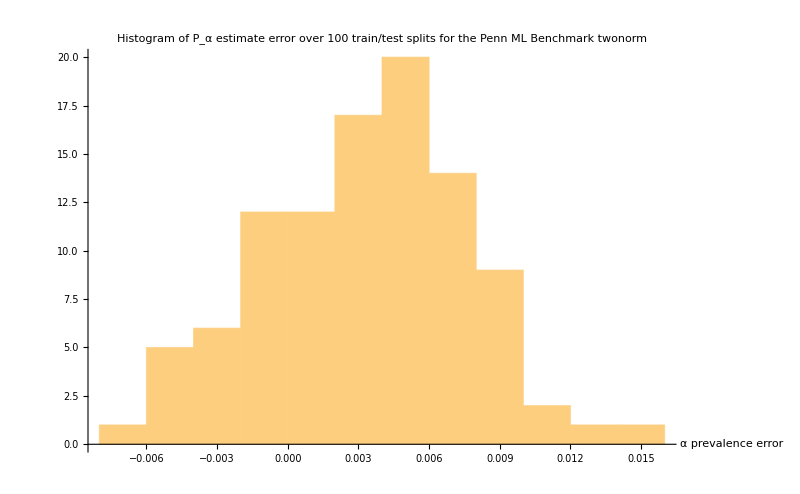

```mathematica
runs//Take[#,3]&/@#&//Transpose//First//
Histogram[#,PlotLabel->"Histogram of P_α estimate error over 100 train/test splits\nfor the Penn ML Benchmark twonorm",
AxesLabel->{"α prevalence error",None},
BaseStyle->{FontSize->14},ImageSize->800]&
```

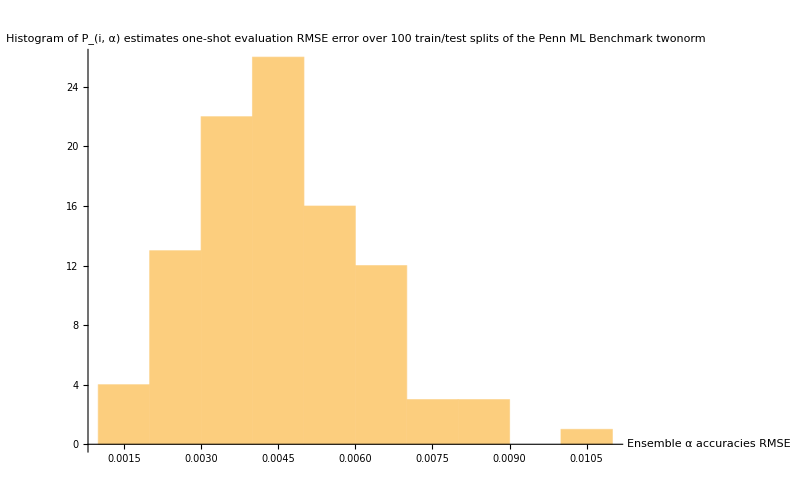

```mathematica
runs//Take[#,3]&/@#&//Transpose//#[[2]]&//
Histogram[#,PlotLabel->"Histogram of P_(i, α) estimates one-shot evaluation RMSE error over \n100 train/test splits of the Penn ML Benchmark twonorm",
AxesLabel->{"Ensemble α accuracies RMSE",None},
BaseStyle->{FontSize->14},ImageSize->800]&
```

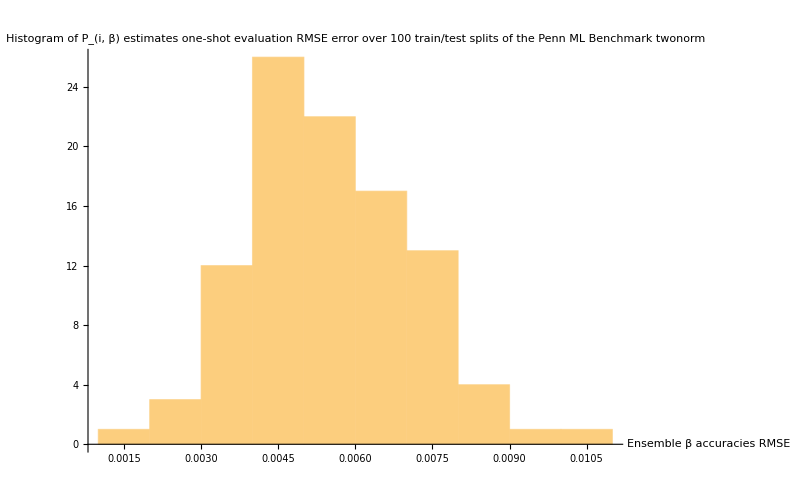

```mathematica
runs//Transpose//#[[3]]&//
Histogram[#,PlotLabel->"Histogram of P_(i, β) estimates one-shot evaluation RMSE error over \n100 train/test splits of the Penn ML Benchmark twonorm",
AxesLabel->{"Ensemble β accuracies RMSE",None},
BaseStyle->{FontSize->14},ImageSize->800]&
```